```mathematica
n=20;
f[u_]:=Sum[Exp[ⅈ u j],{j,1,n}]
```

```mathematica
j=3;
1/(2π) Integrate[(ⅈ/2 Cot[x/2]+π DiracDelta[x]) Exp[-j ⅈ x],{x,-π,π},PrincipalValue->True]
Clear[j]
```

1

```mathematica
gf[x_]:=ⅈ/2 Cot[x/2]+π DiracDelta[x]-1/2
```

```mathematica
Integrate[Sin[x-1]^2 gf[x],{x,-π,π},PrincipalValue->True]//N
```

0.653682-1.42832 ⅈ

```mathematica
S[w_]:=1/3+1/2 Exp[ⅈ w]+Sin[w]+1/7 Sin[2 w]
U[x_]:=NIntegrate[S[x+w] S[w],{w,-π,π}]
```

```mathematica
U[x_]:=Sech[x+1]
```

```mathematica
Clear[U,S]
```

```mathematica
U[1]
```

5.10278-0.0143017 ⅈ

```mathematica
1/(2π) NIntegrate[U[x] gf[x],{x,-π,π},Method->"PrincipalValue",Exclusions->{0}]
```

-0.22886-0.215075 ⅈ

```mathematica
aveInt[f_]:=1/(2π) NIntegrate[f,{x,-π,π},Method->"PrincipalValue",Exclusions->{0}]
```

```mathematica
Sum[Abs[1/(2π)NIntegrate[S[w] Exp[ⅈ w j],{w,-π,π}]]^2,{j,1,30}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {1.12896}. NIntegrate obtained -4.45824×10^-16 + 1.10675×10^-15\ ⅈ and 3.81538×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {5.6345×10^-8}. NIntegrate obtained 4.75314×10^-16 - 5.63785×10^-17\ ⅈ and 6.61201×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {5.6345×10^-8}. NIntegrate obtained -8.32667×10^-17 - 4.38885×10^-16\ ⅈ and 7.33323×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

0.255102

```mathematica
U[u_]:=1/(2 π) Integrate[S[u+w] Conjugate[S[w]],{w,-π,π}]
```

```mathematica
aveInt[U[x] gf[x]]+1/(2π) N[Integrate[U[x] π DiracDelta[x],{x,-π,π}]]
```

0.255102+0. ⅈ

```mathematica
aveInt[U[x] (ⅈ/2 Cot[x/2])]+1/2 aveInt[S[x] Conjugate[S[x]]]-1/2 Abs[aveInt[S[x]]]^2
```

0.255102-4.41744×10^-18 ⅈ

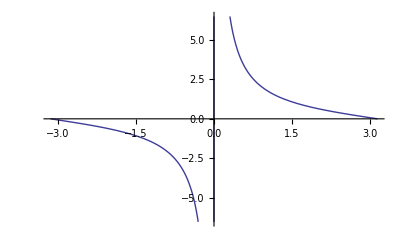

```mathematica
Plot[Cot[x/2],{x,-π,π}]
```

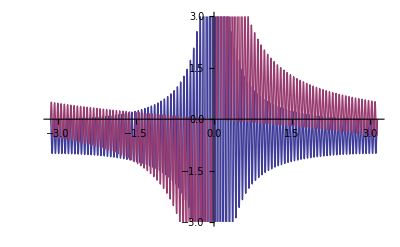

```mathematica
Plot[{Re[f[x]],Im[f[x]]},{x,-π,π},PlotRange->{-3,3}]
```

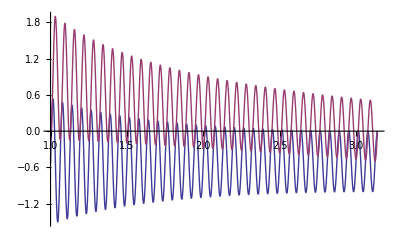

```mathematica
Plot[{Re[f[x]],Im[f[x]]},{x,1,π},PlotRange->All]
```